## Linearized continuity equation

```mathematica
Solve[-ⅈ ω ρ1[r]+1/r^2 D[(r^2 ρ0[r]u1[r]), r]==0,ρ1[r]]
```

{{ρ1[r]→(ⅈ (-2 u1[r] ρ0[r]-r ρ0[r] u1'[r]-r u1[r] ρ0'[r]))/(r ω)}}

## General linearized momentum equation

```mathematica
viscousTerm=1/r^2 D[(μ[r]D[(r^2 u1[r]), r]), r];
ρ1Linear[r_]:=(ⅈ (-2 u1[r] ρ0[r]-r ρ0[r] u1'[r]-r u1[r] ρ0'[r]))/(r ω)
Feqn0=-ⅈ ω ρ0[r]u1[r]+cs2[r]ρ1'[r]+ρ1[r]g[r]-viscousTerm;
Feqn1=(-1/(r^2 ω)ⅈ )^-1 Feqn0/.ρ1->ρ1Linear//FullSimplify
```

r (u1'[r] ((2 cs2[r]+r g[r]) ρ0[r]-ⅈ ω (4 μ[r]+r μ'[r])+2 r cs2[r] ρ0'[r])+r (-ⅈ ω μ[r]+cs2[r] ρ0[r]) u1''[r])+u1[r] (-2 ⅈ ω μ[r]+(r^2 ω^2-2 cs2[r]+2 r g[r]) ρ0[r]+r (-2 ⅈ ω μ'[r]+(2 cs2[r]+r g[r]) ρ0'[r]+r cs2[r] ρ0''[r]))

## Common assumptions

```mathematica
pointMassGravity=g->((G M)/#^2&);
virialized=cs2->(1/α(G M)/#&);
powerLawDensity=ρ0->(ρb(#/r0)^-α&);
constantViscosity=μ->Function[r,ρ0[r]ν];
u1diffvec={u1[r],u1'[r],u1''[r]};
nondimensionlized={G->ω^2/(M k0^3),ν-> ω k1/k0^3};
wkbApproximation={u1->Function[r,A[r] ⅇ^(ⅈ ϕ[r])],ϕ'[r]->ω/√cs2[r],ϕ''[r]->0};
```

## Inviscid α=3/2 atmosphere

```mathematica
system=(r α)/((r/r0)^-α ρb)Feqn1//.{pointMassGravity,virialized,powerLawDensity,constantViscosity,ν->0,α->3/2};
Coefficient[system,#]&/@u1diffvec//FullSimplify//MatrixForm
DSolve[system==0,u1,r]//FullSimplify
```

(1/2 (-G M+3 r^3 ω^2)
(G M r)/2
G M r^2)

{{u1→Function[{r},(ⅇ^((ⅈ √(2/3) r^(3/2) ω)/(√G √M)) C[1])/(√r)+(ⅈ ⅇ^(-(ⅈ √(2/3) r^(3/2) ω)/(√G √M)) √G √M C[2])/(√6 √r ω)]}}

## Constant viscosity α=3/2 atmosphere

```mathematica
system=12/(ρb ω^2) k0^3 r (r/r0)^(3/2)Feqn1//.{pointMassGravity,virialized,powerLawDensity,constantViscosity,α->3/2}~Join~nondimensionlized;
Coefficient[system,#]&/@u1diffvec//FullSimplify//MatrixForm
```

(4 (-1+3 ⅈ k1 r+3 k0^3 r^3)
2 r (2-15 ⅈ k1 r)
4 r^2 (2-3 ⅈ k1 r))

### It is possible to iterate to find the BC which approximately selects the outgoing wave:

InterpolatingFunction[…]

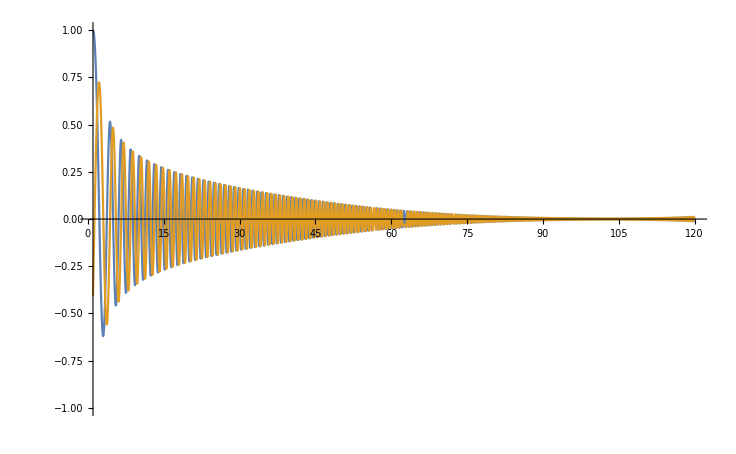

```mathematica
soln=u1/.First@NDSolve[{
FullSimplify[system]==0,
u1[1]==1-0.409ⅈ,
u1'[1]==1.430ⅈ}/.{k0->1,k1->0.0001},u1,{r,1,200}]
Plot[{Re@soln[r],Im@soln[r]},{r,1,120},PlotRange->{{1,120},{-1,1}}]
```

## Linearized continuity equation (planar)

```mathematica
(*Solve[-ⅈ ω ρ1[x]+∂_x (ρ0[x]u1[x])==0,ρ1[x]]*)
```

## General linearized momentum equation (planar)

```mathematica
(*viscousTerm=∂_x (μ[x]∂_x (u1[x]));
ρ1Linear[x_]:=(ⅈ (-ρ0[x] u1'[x]-u1[x] ρ0'[x]))/ω
planarAssumptions={constantViscosity,ρ0->Function[x,ρ],cs2->Function[x,a2]};
Feqn0=-ⅈ ω ρ0[x]u1[x]+cs2[x]ρ1'[x]-viscousTerm;
Feqn1=Feqn0/.ρ1->ρ1Linear//FullSimplify;
system=-ω/(ρ ⅈ)Feqn1//.planarAssumptions//Simplify
soln=u1/.First@NDSolve[{system==0,u1[0]==1,u1'[0]==1.97085ⅈ}/.{a2->1,ω->2,ν->0.1},u1,{x,0,20}]
Plot[{Re@soln[x],Im@soln[x]},{x,0,20}]*)
```

```mathematica
(*u1/.First@DSolve[system==0,u1,x]*)
```

```mathematica
(*Plot[Im@(ⅇ^((x ω)/(√(-a2+ⅈ ν ω))) C[1]+ⅇ^(-(x ω)/(√(-a2+ⅈ ν ω))) C[2])/.{C[1]->0.0,C[2]->1,a2->1,ω->2,ν->0.1},{x,0,20}]*)
```

```mathematica
(*ρ1Linear[x]/u1[x]/.First@DSolve[system==0,u1,x]/.planarAssumptions/.C[1]->0//FullSimplify*)
```

## WKB approach

```mathematica
k1/(4 r^2 (2-3 ⅈ k1 r))system//Expand//FullSimplify
```

(-2 k1 (ⅈ+3 k1 r-3 ⅈ k0^3 r^3) u1[r]+k1 r (2 ⅈ+15 k1 r) u1'[r])/(2 r^2 (2 ⅈ+3 k1 r))+k1 u1''[r]

```mathematica
Coefficient[(-2 k1 (ⅈ+3 k1 r-3 ⅈ k0^3 r^3) u1[r]+k1 r (2 ⅈ+15 k1 r) u1'[r])/(2 r^2 (2 ⅈ+3 k1 r)),u1[r]]
Coefficient[(-2 k1 (ⅈ+3 k1 r-3 ⅈ k0^3 r^3) u1[r]+k1 r (2 ⅈ+15 k1 r) u1'[r])/(2 r^2 (2 ⅈ+3 k1 r)),u1'[r]]
```

-(k1 (ⅈ+3 k1 r-3 ⅈ k0^3 r^3))/(r^2 (2 ⅈ+3 k1 r))

(k1 (2 ⅈ+15 k1 r))/(2 r (2 ⅈ+3 k1 r))

```mathematica
1/Exp[1/δ(S0[r]+S1[r]δ)](f[r]u[r]+g[r]u'[r]+ϵ^2 u''[r])/.u->Function[r,Exp[1/δ(S0[r]+S1[r]δ)]]//FullSimplify//Expand
```

f[r]+(g[r] S0'[r])/δ+(ϵ^2 S0'[r]^2)/δ^2+g[r] S1'[r]+(2 ϵ^2 S0'[r] S1'[r])/δ+ϵ^2 S1'[r]^2+(ϵ^2 S0''[r])/δ+ϵ^2 S1''[r]

```mathematica
Solve[f[r]+(ϵ^2 S0'[r]^2)/δ^2==0,S0'[r]]
```

{{S0'[r]→-(ⅈ δ √f[r])/ϵ},{S0'[r]→(ⅈ δ √f[r])/ϵ}}

```mathematica
(√f[r])/δ(f[r]+(g[r] S0'[r])/δ+(ϵ^2 S0'[r]^2)/δ^2+g[r] S1'[r]+(2 ϵ^2 S0'[r] S1'[r])/δ+ϵ^2 S1'[r]^2+(ϵ^2 S0''[r])/δ+ϵ^2 S1''[r])//.{S0'[r]->(ⅈ δ √f[r])/ϵ,S0''[r]->D[((ⅈ δ √f[r])/ϵ), r],ϵ->δ}//FullSimplify
```

1/2 ⅈ f'[r]+(ⅈ f[r] (g[r]+2 δ^2 S1'[r]))/δ^2+√f[r] ((g[r] S1'[r])/δ+δ (S1'[r]^2+S1''[r]))